```mathematica
f1=x2[t]
deq1= x1'[t]==f1

f2=x1[t]-x1[t]^3
deq2=x2'[t]==f2
```

x2[t]

x1'[t]==x2[t]

x1[t]-x1[t]^3

x2'[t]==x1[t]-x1[t]^3

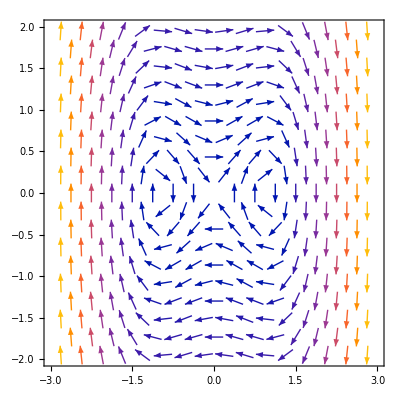

```mathematica
gr1=VectorPlot[{f1,f2},{x1[t],-3,3},{x2[t],-2,2}]
```

```mathematica
trange=3;
x10=3;x20=0;
sol1=NDSolve[{deq1,deq2,x1[0]==x10,x2[0]==x20},{x1,x2},{t,-trange,trange}]
x1t=x1[t]/.sol1[[1]]
x2t=x2[t]/.sol1[[1]]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

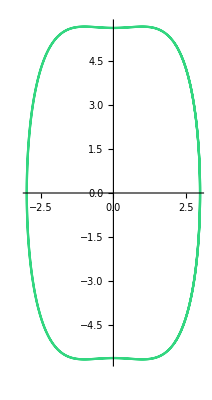

```mathematica
gr2=ParametricPlot[{x1t,x2t},{t,-trange,trange},PlotStyle-> RGBColor[0.2,0.84,0.5]]
```

```mathematica
f1=x2[t]
deq1= x1'[t]==f1

f2=-x1[t]+x1[t]^3
deq2=x2'[t]==f2
```

x2[t]

x1'[t]==x2[t]

-x1[t]+x1[t]^3

x2'[t]==-x1[t]+x1[t]^3

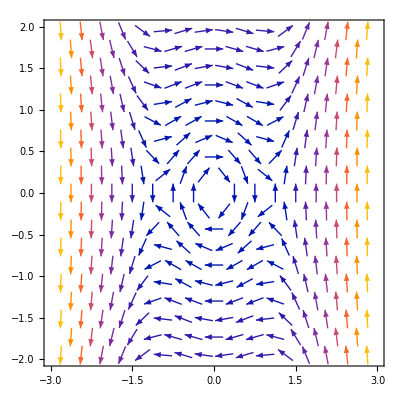

```mathematica
gr3=VectorPlot[{f1,f2},{x1[t],-3,3},{x2[t],-2,2}]
```

```mathematica
trange=1;
x10=1;x20=0;
sol1=NDSolve[{deq1,deq2,x1[0]==x10,x2[0]==x20},{x1,x2},{t,-trange,trange}]
x1t=x1[t]/.sol1[[1]]
x2t=x2[t]/.sol1[[1]]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

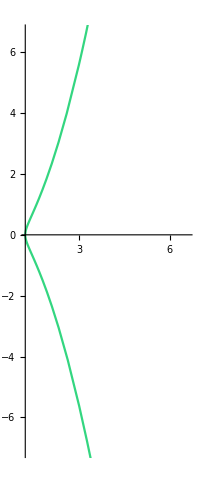

```mathematica
gr4=ParametricPlot[{x1t,x2t},{t,-trange,trange},PlotStyle-> RGBColor[0.2,0.84,0.5]]
```

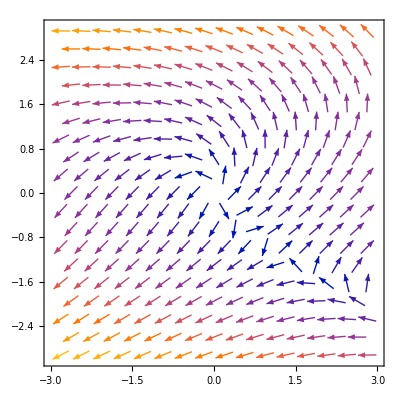

```mathematica
f1=x1-x2^2;
f2=x1+x2;
gr1=VectorPlot[{f1,f2},{x1,-3,3},{x2,-3,3}]
```

```mathematica
eqsol=Solve[{f1==0,f2==0},{x1,x2}](*Σημεία ισορροπίας*)
```

{{x1→1,x2→-1},{x1→0,x2→0}}

{1,-1}

{0,0}

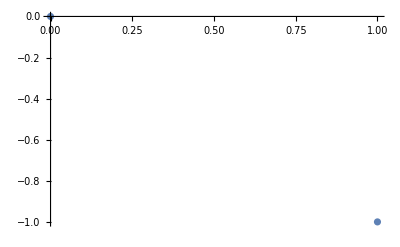

```mathematica
P1={x1,x2}/.eqsol[[1]]
P2={x1,x2}/.eqsol[[2]]
gr2=ListPlot[{P1,P2},PlotStyle->Thick]
```

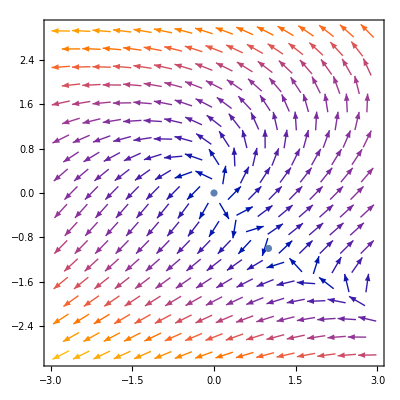

```mathematica
Show[gr1,gr2]
```

```mathematica
f1t=f1/.{x1->x1[t],x2->x2[t]};
f2t=f2/.{x1->x1[t],x2->x2[t]};
deq1=x1'[t]==f1t
deq2=x2'[t]==f2t
```

x1'[t]==x1[t]-x2[t]^2

```mathematica
x2'[t]==x1[t]+x2[t]

trange=1
x10=1;x20=0
```

x2'[t]==x1[t]+x2[t]

1

0

```mathematica
sol1=NDSolve[{deq1,deq2,x1[0]==x10,x2[0]==x20},{x1,x2},{t,1,2}]
```

```mathematica
{{x1->InterpolatingFunction[…],x2->InterpolatingFunction[…]}}
x1t=x1[t]/.sol1[[1]]
x2t=x2[t]/.sol1[[1]]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…]}}

InterpolatingFunction[…][t]

InterpolatingFunction[…][t]

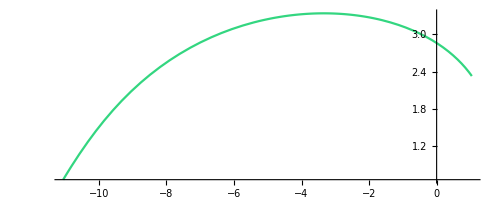

```mathematica
gr3=ParametricPlot[{x1t,x2t},{t,1,2},PlotStyle-> RGBColor[0.2,0.84,0.5]]
```

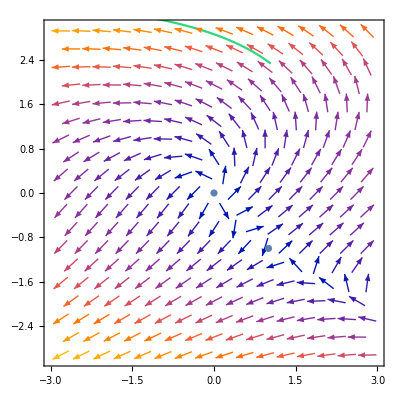

```mathematica
Show[gr1,gr2,gr3]
```

```mathematica
f1=x2
f2[t_]=x1*Sin[t]-x1^3
```

x2

-x1^3+x1 Sin[t]

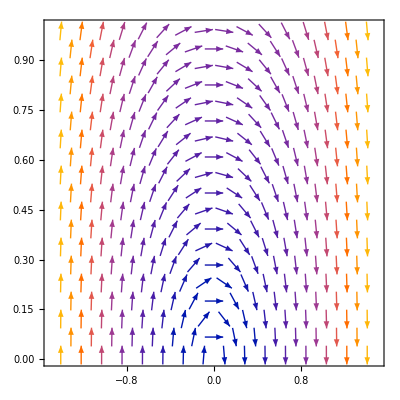

```mathematica
gr1=VectorPlot[{f1,f2[12]},{x1,-1.5,1.5},{x2,0,1}]
```

```mathematica
Monitor[For[t=-1,t<5,{tt=VectorPlot[{f1,f2[t]},{x1,-1.5,1.5},{x2,-1,1}],Pause[0.5]},t=t+0.3],tt]
```